# Audio Classification

## Data gathering

```mathematica
meta=<|"T1DepDIFAdat7_OM"->{"Bottom","Deploy"},
"T1MidDIFAdat7_OM"->{"Bottom","Midtrawl"},
"T1RecDIFAdat7_OM"->{"Bottom","Recovery"},
"T2DepDIFAdat7_OM"->{"Midwater","Deploy"},
"T2MidDIFAdat7_OM"->{"Midwater","Midtrawl"},
"T2RecDIFAdat7_OM"->{"Midwater","Recovery"}|>;
```

```mathematica
files=FileNames["*.wav",NotebookDirectory[]]
```

{C:\Users\msoll\Dropbox\mac-pc\T1DepDIFAdat7_OM.wav,C:\Users\msoll\Dropbox\mac-pc\T1MidDIFAdat7_OM.wav,C:\Users\msoll\Dropbox\mac-pc\T1RecDIFAdat7_OM.wav,C:\Users\msoll\Dropbox\mac-pc\T2DepDIFAdat7_OM.wav,C:\Users\msoll\Dropbox\mac-pc\T2MidDIFAdat7_OM.wav,C:\Users\msoll\Dropbox\mac-pc\T2RecDIFAdat7_OM.wav}

```mathematica
sounds=(Import/@files);
```

```mathematica
trimmed=AudioTrim[#,{60,AudioMeasurements[#,"Duration"]-60}]&/@sounds;
```

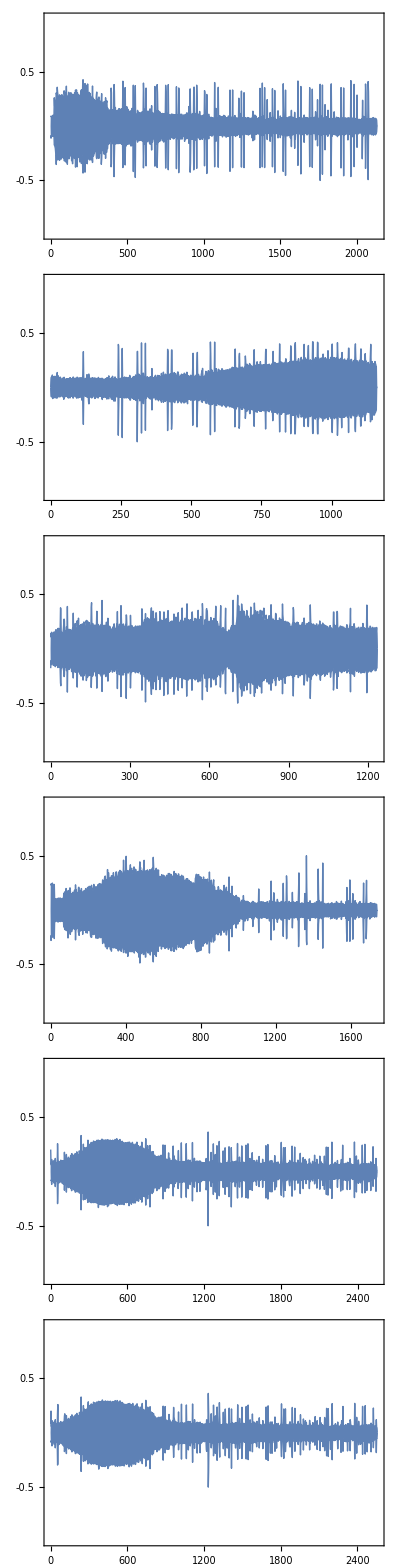

```mathematica
Column[AudioPlot[#,ImageSize->400]&/@sounds]
```

```mathematica
AudioMeasurements[#,{"Length", "SampleRate", "Type"},"Dataset"]&/@sounds
```

{Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>]}

```mathematica
AudioLength/@sounds
```

{34182486 samples,18605398 samples,19765931 samples,27877376 samples,40884347 samples,40898560 samples}

```mathematica
sampleLength=1;
```

```mathematica
samples=AudioPartition[#,sampleLength]&/*Most/@sounds;
```

```mathematica
DumpSave["samples1.mx",samples];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\msoll\Dropbox\mac-pc

```mathematica
Get["samples1.mx"]
```

```mathematica
Length/@samples
```

{2136,1162,1235,1742,2555,2556}

```mathematica
SetDirectory["C:\\Users\\msoll\\Downloads\\Fishackathon-master\\Fishackathon-master\\sounds"]
```

C:\Users\msoll\Downloads\Fishackathon-master\Fishackathon-master\sounds

```mathematica
files=FileNames["*"]
```

{22__19_07_13_adventure_maniobra.wav,6__10_07_13_marDeCangas_Entra.wav,79__23_07_13_H3_zodiac.wav,82__27_09_13_H3_lluvia.wav,Alaska state ferry_Oct_02_2000@101413.mp3,atlantic-spotted-dolphin.ogg,atlantic-white-sided-dolphin.ogg,beaked-whale.ogg,bearded-seal.ogg,beluga-whale.ogg,blue-whale.ogg,bottlenose-dolphin.ogg,cod.ogg,crabeater-seal.ogg,cruise ship_Sep_19_2000@185357.mp3,fin-whale.ogg,freighter_nearing_dock_Oct_31_2001@093754.mp3,gray-seal.ogg,haddock.ogg,harbor-porpoise.ogg,harbor-seal.ogg,harp-seal.ogg,heavy_rain_Aug_12_2002@064500.mp3,humpback-whale.ogg,killer-whale.ogg,leopard-seal.ogg,light_north_wind_Aug_31_2000@103356.mp3,light_rain_Nov_13_2000@143551.mp3,minke-whale.ogg,north-atlantic-right-whale.ogg,oil-and-gas-industries.ogg,Outboard_60hp_@10knots.mp3,Outboard_60hp_@20knots.mp3,pilot-whale.ogg,rissos-dolphin.ogg,ross-seal.ogg,sei-whale.ogg,short-beaked-common-dolphin.ogg,small_diesel_Nov_01_2000@085906-2.mp3,small_diesel_Nov_01_2000@085906.mp3,snowfall_Oct_02_2000@152745.mp3,sperm-whale.ogg,striped-dolphin.ogg,vessel.ogg,weddell-seal.ogg,whining propeller_Jun_27_2001@095655.mp3,white-beaked-dolphin.ogg,windy_afternoon_with_ship_Aug_25_2000@172622.mp3,windy_fallday_Oct_19_2000@113206.mp3}

```mathematica
files={"Alaska state ferry_Oct_02_2000@101413.mp3","atlantic-spotted-dolphin.ogg","atlantic-white-sided-dolphin.ogg","beaked-whale.ogg","bearded-seal.ogg","beluga-whale.ogg","blue-whale.ogg","bottlenose-dolphin.ogg","cod.ogg","crabeater-seal.ogg","cruise ship_Sep_19_2000@185357.mp3","fin-whale.ogg","freighter_nearing_dock_Oct_31_2001@093754.mp3","gray-seal.ogg","haddock.ogg","harbor-porpoise.ogg","harbor-seal.ogg","harp-seal.ogg","heavy_rain_Aug_12_2002@064500.mp3","humpback-whale.ogg","killer-whale.ogg","leopard-seal.ogg","light_north_wind_Aug_31_2000@103356.mp3","light_rain_Nov_13_2000@143551.mp3","minke-whale.ogg","north-atlantic-right-whale.ogg","oil-and-gas-industries.ogg","Outboard_60hp_@10knots.mp3","Outboard_60hp_@20knots.mp3","pilot-whale.ogg","rissos-dolphin.ogg","ross-seal.ogg","sei-whale.ogg","short-beaked-common-dolphin.ogg","small_diesel_Nov_01_2000@085906-2.mp3","small_diesel_Nov_01_2000@085906.mp3","snowfall_Oct_02_2000@152745.mp3","sperm-whale.ogg","striped-dolphin.ogg","vessel.ogg","weddell-seal.ogg","whining propeller_Jun_27_2001@095655.mp3","white-beaked-dolphin.ogg","windy_afternoon_with_ship_Aug_25_2000@172622.mp3","windy_fallday_Oct_19_2000@113206.mp3"};
```

```mathematica
noise=Import[#,"Audio"]&/@files;
```

```mathematica
noise=AudioResample[#,1600]&/@noise;
```

```mathematica
sampleLength=1;
```

```mathematica
noiseSamples=Flatten[AudioPartition[#,1,.25]&/*Most/@noise];
```

```mathematica
noiseSamples//Length
```

4604

```mathematica
bottom=RandomSample[Join@@samples[[1;;3]]];
mid=RandomSample[Join@@samples[[4;;6]]];
noise=RandomSample[noiseSamples];(*Arel can add this isa todo for future fucntions!!!!!*)
```

```mathematica
Length/@{bottom,mid}
```

{4533,6853}

```mathematica
Min[Length/@{bottom,mid}]
```

4533

## Classifier with Noise

```mathematica
train=<|"Bottom"->bottom[[;;4000]],"Midwater"->mid[[;;4000]],"Noise"->noise[[;;4000]]|>;
```

```mathematica
Length/@train
```

<|Bottom→4000,Midwater→4000,Noise→4000|>

```mathematica
test=<|"Bottom"->bottom[[4001;;4533]],"Midwater"->mid[[4001;;4533]],"Noise"->noise[[4001;;4533]]|>;
```

```mathematica
Length/@test
```

<|Bottom→533,Midwater→533,Noise→533|>

```mathematica
net=NetChain[{
GatedRecurrentLayer[64],
DropoutLayer[0.2],
GatedRecurrentLayer[32],
DropoutLayer[0.2],
SequenceLastLayer[],
LinearLayer[],
SoftmaxLayer[]},
"Input"->NetEncoder[{"AudioSpectrogram"}],
"Output"->NetDecoder[{"Class",{"Bottom","Midwater","Noise"}}]]
```

NetChain[<>]

```mathematica
trainData1=Join[Thread[train["Bottom"]->"Bottom"],Thread[train["Midwater"]->"Midwater"],Thread[train["Noise"]->"Noise"]];
testData1=Join[Thread[test["Bottom"]->"Bottom"],Thread[test["Midwater"]->"Midwater"],Thread[test["Noise"]->"Noise"]];
```

```mathematica
Dimensions@trainData1
```

{12000}

```mathematica
Dimensions@testData1
```

{1599}

```mathematica
results=NetTrain[net,trainData1,All,ValidationSet->testData1,MaxTrainingRounds->100,TargetDevice->"GPU"]
```

NetTrainResultsObject[<>]

```mathematica
net=results["TrainedNet"]
```

NetChain[<>]

```mathematica
Quit[]
```

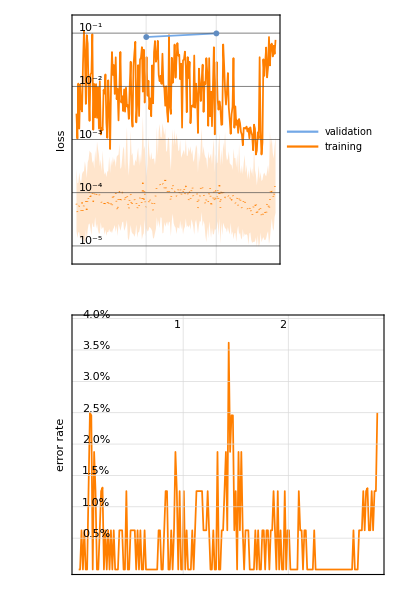

```mathematica
plots=results["EvolutionPlots"]
```

```mathematica
results["TrainingNet"]
```

NetGraph[<>]

```mathematica
Labeled[results[#],#]&/@results["Properties"]
```

```mathematica
cl5=ClassifierMeasurements[trainedNet,testData1]
cl5["Accuracy"]
```

ClassifierMeasurementsObject[…]

0.986867

```mathematica
NotebookDirectory[]
```

C:\Users\msoll\Dropbox\mac-pc\

```mathematica
(*Export["C:\\Users\\msoll\\Downloads\\net_98.wlnet",trainedNet]*)
```

C:\Users\msoll\Downloads\net_98.wlnet

```mathematica
NotebookDirectory[]
```

C:\Users\msoll\Dropbox\mac-pc\

```mathematica
cl5["ConfusionMatrix"]
```

{{520,12,1,0},{8,525,0,0},{0,0,533,0}}

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"confusion.pdf"}],cl5["ConfusionMatrixPlot"]]
```

C:\Users\msoll\Dropbox\mac-pc\confusion.pdf

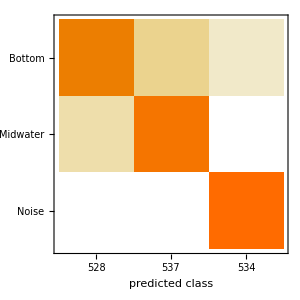

```mathematica
func=APIFunction[{"a"->"Audio"},a↦trainedNet@a]
```

APIFunction[{a→Audio},Function[a,trainedNet[a]]]

```mathematica
api=CloudDeploy[func,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/3b1b8481-ff76-4088-b4f5-663846b4cab2]

```mathematica
CloudDeploy[FormPage[{{"ex","Upload WAV file:"}->"UploadedFile"},AudioPlot@Import[#ex]&]]
```

CloudObject[https://www.wolframcloud.com/objects/01e32afc-5be4-4ac7-a82c-7494f4b6fd00]

```mathematica
CloudDeploy[APIFunction[{{"ex","Upload WAV file:"}->"UploadedFile"},AudioPlot@Import[#ex]&]]
```

CloudObject[https://www.wolframcloud.com/objects/07d762d2-f7db-483f-b7c1-0eda7a91ce25]

```mathematica
CloudDeploy[APIFunction[{{"ex","Sound"->Audio[]}->"UploadedFile"},AudioPlot@Import[#ex]&]]
```

CloudObject[https://www.wolframcloud.com/objects/79bc8225-d29f-49f2-9959-210bc652ceea]